## AKLT

AKLT is an anti-ferromagnetic model. (Q: what is the single spin expectation value? zero?)

Summary: PBC
(1)For AKLT model with PBC, the ground state is in Haldane phase. The ground state can be represented using matrix product state, and the correlation length can be shown analytically to be  1/(log(3)). 
Note that ⟨S_z^i S_z^j⟩≈-4/3^(|i-j|+2) for i-j being even, and ⟨S_z^i S_z^j⟩≈4/3^(|i-j|+2) for i-j being odd. This seems to show the anti-ferromagnetic property
(2)Note the unique ground state is translational invariant (true for integer spin s). If we use half-integer spin, the ground state would break translational symmetry, namely, it is dimerized. We thus have degenerate ground state.

#### Trace

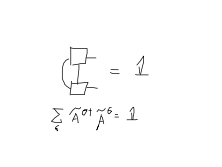
The construction comes from:
-Graphics-
here Σ=(0 | √1/2
-√1/2  | 0) which comes from the spin singlet, 
and M^[-1]=(0 | 0
0  | 1), M^[0]=(0 | √1/2
√1/2  | 0), M^[1]=(1 | 0
0  | 0) come from projection to spin one
Thus in MPS representation, we have (Ã)^[-1]=(0 | 0
-√2/3  | 0), (Ã)^[0]=(-√1/3 | 0
0  | √1/3), (Ã)^[1]=(0 | √2/3
0  | 0) after left normalization. 
Left normalization means
-Graphics-

We can rewrite the MPS using the following grouping:  
-Graphics-

```mathematica
Eigensystem[A]
```

{{1,-1/3,-1/3,-1/3},{{1,0,0,1},{-1,0,0,1},{0,0,1,0},{0,1,0,0}}}

```mathematica
A//MatrixForm
```

(1/3 | 0 | 0 | 2/3
0 | -1/3 | 0 | 0
0 | 0 | -1/3 | 0
2/3 | 0 | 0 | 1/3)

```mathematica
A={{1/3,0,0,2/3},{0,-1/3,0,0},{0,0,-1/3,0},{2/3,0,0,1/3}};
```

```mathematica
AS={{0,0,0,-2/3},{0,0,0,0},{0,0,0,0},{2/3,0,0,0}}; (*Sz inserted*)
```

A^n=((3^n+1)/(2 3^n) | 0 | 0 | (3^n-1)/(2 3^n)
0 | 1/3^n | 0 | 0
0 | 0 | 1/3^n | 0
(3^n-1)/(2 3^n) | 0 | 0 | (3^n+1)/(2 3^n)) for n being even.
This can be easily shown using recursion.
The trace is thus: tr(A^n)=(3^(n-1)+1)/3^(n-1) 
For n being odd, we have:
A^n=((3^n-1)/(2 3^n) | 0 | 0 | (3^n+1)/(2 3^n)
0 | -1/3^n | 0 | 0
0 | 0 | -1/3^n | 0
(3^n+1)/(2 3^n) | 0 | 0 | (3^n-1)/(2 3^n)),
and the trace is: tr(A^n)=(3^(n-1)-1)/3^(n-1)

```mathematica
MatrixPower[A,3]//MatrixForm;
```

#### Spin correlation

```mathematica
bSite=101;
spinEpt=N[Tr[MatrixPower[A,bSite].AS.MatrixPower[A,bSite]]]
```

0.

```mathematica
data = Transpose[{xRange,Log[Abs[spinC]]}];
lm=LinearModelFit[data,x,x]
Show[ListPlot[data],Plot[lm[x],{x,2,20}]]
```

```mathematica
-Graphics-   n=Sep/2,m=bSite-n=bSite-Sep/2
```

One can show:
A^n.S.A^n=(0 | 0 | 0 | -2/3^(n+1)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-2/3^(n+1) | 0 | 0 | 0),
thus the above expression equals to:
⟨S_z^i S_z^j⟩=(-4(3^(2m)+1))/3^(2n+2+2m)≈-4/3^(2n+2)=-4/3^(|i-j|+2)
This shows that the correlation length is ξ=1/Log[3].

```mathematica
AN[n_]:=({{(3^n+1)/(2 3^n), 0, 0, (3^n-1)/(2 3^n)}, {0, 1/3^n, 0, 0}, {0, 0, 1/3^n, 0}, {(3^n-1)/(2 3^n), 0, 0, (3^n+1)/(2 3^n)}});
```

```mathematica
AN[n].AS.AN[n]//Simplify//MatrixForm
```

(0 | 0 | 0 | -2 3^(-1-n)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
2 3^(-1-n) | 0 | 0 | 0)

```mathematica
bSite=100;
spinCorr[sep_]:=N[Tr[MatrixPower[A,bSite].AS.MatrixPower[A,sep].AS.MatrixPower[A,bSite]]]
(*xRange = Range[2,20,2];*)
xRange = Range[1,20,1];
spinC=Table[spinCorr[sep],{sep,xRange}]
```

{0.148148,-0.0493827,0.0164609,-0.00548697,0.00182899,-0.000609663,0.000203221,-0.0000677404,0.0000225801,-7.52671×10^-6,2.5089×10^-6,-8.36301×10^-7,2.78767×10^-7,-9.29223×10^-8,3.09741×10^-8,-1.03247×10^-8,3.44157×10^-9,-1.14719×10^-9,3.82396×10^-10,-1.27465×10^-10}

FittedModel[-0.81093-1.09861 x]

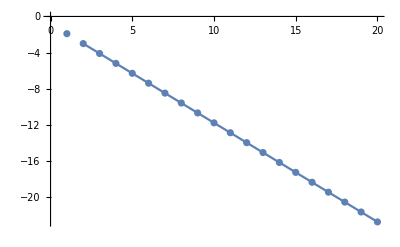

```mathematica
data = Transpose[{xRange,Log[Abs[spinC]]}];
lm=LinearModelFit[data,x,x]
Show[ListPlot[data],Plot[lm[x],{x,2,20}]]
```

```mathematica
N[Log[3]]
```

1.09861

```mathematica
N[Log[9/4]]
```

0.81093

### Entanglement

-Graphics-
For the MPS representation, for the open chain, the entanglement can be computed easily using orthogonal center. The computation amounts to finding the Schmidt decomposition of the state:
	|ψ⟩ = ∑_λ p_λ|L_λ⟩|R_λ⟩
And:
	S = -  ∑_λ (p_λ)^2 log(p_λ^2).
Thus if the bond dimension is D, the upper bound of S is:
	S_max=log D.

Here, a hand-wavy argument is that, for the PBC chain, there are two entanglement cuts, so the upper bound is S_max=2log D=2log 2, which turns out to be the value of S in large chain limit, agrees with the result in [https://arxiv.org/pdf/0802.3221.pdf]. 

(Can we have a more analytical argument for this?)

- If instead, we compute the single-site entanglement, the result is log(3). This is because for single-site, spin-1 (3-dim) must be totally disordered (as we are in SPT, it’s spin-rotation symmetric)

- Also check [https://arxiv.org/pdf/cond-mat/0505140.pdf]

```mathematica
Am=({{0, 0}, {-√2/3, 0}}); A0=({{-√1/3, 0}, {0, √1/3}}); Ap=({{0, √2/3}, {0, 0}});
Atot={Ap,A0,Am};
```

```mathematica
KroneckerProduct[Am,Am]+KroneckerProduct[A0,A0]+KroneckerProduct[Ap,Ap]
```

{{1/3,0,0,2/3},{0,-1/3,0,0},{0,0,-1/3,0},{2/3,0,0,1/3}}

```mathematica
KroneckerProduct[Am,Am]-KroneckerProduct[Ap,Ap]
```

{{0,0,0,-2/3},{0,0,0,0},{0,0,0,0},{2/3,0,0,0}}

```mathematica
test=Transpose[Atot,{2,1,3}];
ARe=ArrayReshape[test,{2,6}];
{u, σ, v} = SingularValueDecomposition[ARe];
σ
```

{{1,0,0,0,0,0},{0,1,0,0,0,0}}

```mathematica
u
```

{{0,1},{1,0}}

```mathematica
v//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 1
0 | √(2/3) | 0 | 0 | 1/(√3) | 0
0 | -1/(√3) | 0 | 0 | √(2/3) | 0
1/(√3) | 0 | 0 | √(2/3) | 0 | 0
-√(2/3) | 0 | 0 | 1/(√3) | 0 | 0
0 | 0 | 1 | 0 | 0 | 0)

```mathematica
v.Transpose[v]
```

{{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}}

```mathematica
ARe//MatrixForm
```

(0 | √(2/3) | -1/(√3) | 0 | 0 | 0
0 | 0 | 0 | 1/(√3) | -√(2/3) | 0)

```mathematica
ARe.Transpose[ARe]
```

{{1,0},{0,1}}

```mathematica
reDM[bs1_,bs2_]:=Tr[AN[n].KroneckerProduct[bs1,bs2]]
```

```mathematica
reDMNm=Table[reDM[Atot[[i]],Atot[[j]]],{i,1,Length[Atot]},{j,1,Length[Atot]}];
reDMNm//MatrixForm//Simplify
```

(1/3 (1-3^-n) | 0 | 0
0 | 1/3 (1-3^-n) | 0
0 | 0 | 1/3 (1-3^-n))

```mathematica
A2tot=Flatten[Table[Atot[[i]].Atot[[j]],{i,1,3},{j,1,3}],1];
reDMNm2=Table[reDM[A2tot[[i]],A2tot[[j]]],{i,1,Length[A2tot]},{j,1,Length[A2tot]}];
reDMNm2//MatrixForm//Simplify
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3^(-2-n) (-1+3^n) | 0 | 1/9 (-1+3^-n) | 0 | 0 | 0 | 0 | 0
0 | 0 | 2/9 (1+3^-n) | 0 | -3^(-2-n) (3+3^n) | 0 | 4 3^(-2-n) | 0 | 0
0 | 1/9 (-1+3^-n) | 0 | 3^(-2-n) (-1+3^n) | 0 | 0 | 0 | 0 | 0
0 | 0 | -3^(-2-n) (3+3^n) | 0 | 1/9+3^(-1-n) | 0 | -3^(-2-n) (3+3^n) | 0 | 0
0 | 0 | 0 | 0 | 0 | 3^(-2-n) (-1+3^n) | 0 | 1/9 (-1+3^-n) | 0
0 | 0 | 4 3^(-2-n) | 0 | -3^(-2-n) (3+3^n) | 0 | 2/9 (1+3^-n) | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/9 (-1+3^-n) | 0 | 3^(-2-n) (-1+3^n) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Eigenvalues[reDMNm2]//Simplify
```

{0,0,0,0,0,2/9 (1-3^-n),2/9 (1-3^-n),2/9 (1-3^-n),1/3+3^-n}

```mathematica
Eigensystem[AN[n]]
```

{{3^-n,3^-n,3^-n,1},{{-1,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,1}}}

```mathematica
N[Log[3]]
```

1.09861

```mathematica
N[2/3*Log[2/9]+1/3*Log[1/3]]
```

-1.36892

```mathematica
N[Log[4]]
```

1.38629

```mathematica
A3tot=Flatten[Table[A2tot[[i]].Atot[[j]],{i,1,3^2},{j,1,3}],1];
reDMNm3=Table[reDM[A3tot[[i]],A3tot[[j]]],{i,1,Length[A3tot]},{j,1,Length[A3tot]}];
Eigenvalues[reDMNm3]//Simplify
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,7 3^(-3-n) (-1+3^n),7 3^(-3-n) (-1+3^n),7 3^(-3-n) (-1+3^n),2/9 (1+3^(1-n))}

```mathematica
N[2/9*Log[2/9]+7/9*Log[7/27]]
```

-1.38418

#### Symmetry

```mathematica
Sx.Sy-Sy.Sx-I Sz
Sy.Sz-Sz.Sy-I Sx
Sz.Sx-Sx.Sz-I Sy
```

{{0,0,0},{0,0,0},{0,0,0}}

{{0,0,0},{0,0,0},{0,0,0}}

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
Sz={{1,0,0},{0,0,0},{0,0,-1}};
Sx=√2/2{{0,1,0},{1,0,1},{0,1,0}};
Sy=-I √2/2{{0,1,0},{-1,0,1},{0,-1,0}};
S={Sx,Sy,Sz};
```

```mathematica
Sx2={{0,1},{1,0}};
Sy2={{0,-I},{I,0}};
Sz2={{1,0},{0,-1}};
S2={Sx2,Sy2,Sz2};

M1={{1,0},{0,0}};
M0=1/(√2){{0,1},{1,0}};
Mm1={{0,0},{0,1}};
M={M1,M0,Mm1};
```

```mathematica
Am=({{0, 0}, {-√2/3, 0}}); A0=({{-√1/3, 0}, {0, √1/3}}); Ap=({{0, √2/3}, {0, 0}});
A={Ap,A0,Am};
```

```mathematica
(*Check the symmetry using M tensor*)
ii=3;
rot=MatrixExp[I (Subscript[θ, 1] S[[ii]])];
Table[Simplify[rot[[row,1]]M1+rot[[row,2]]M0+rot[[row,3]]Mm1//MatrixForm],{row,1,3}]
Table[Simplify[Transpose[MatrixExp[I θ/2 S2[[ii]]]].M[[i]].MatrixExp[I θ/2 S2[[ii]]],Assumptions->{θ>0}]//MatrixForm,{i,1,3}]
```

{(ⅇ^(ⅈ θ_1) | 0
0 | 0),(0 | 1/(√2)
1/(√2) | 0),(0 | 0
0 | ⅇ^(-ⅈ θ_1))}

{(ⅇ^(ⅈ θ) | 0
0 | 0),(0 | 1/(√2)
1/(√2) | 0),(0 | 0
0 | ⅇ^(-ⅈ θ))}

```mathematica
(*Check the symmetry using A tensor*)
ii=3;
rot=MatrixExp[I (θ S[[ii]])];
res1=Table[Simplify[Sum[rot[[row,col]]A[[col]],{col,1,3}]],{row,1,3}];
res2=Table[Simplify[Transpose[MatrixExp[I θ/2 S2[[ii]]]].A[[i]].Conjugate[MatrixExp[I θ/2 S2[[ii]]]],Assumptions->{θ>0}],{i,1,3}];
res1-res2//Simplify
```

{{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}}}

```mathematica
sig={{0,1},{-1,0}};
rot2=MatrixExp[I (Subscript[θ, 1] Sx2+Subscript[θ, 2] Sy2+Subscript[θ, 3] Sz2)];
rot22=Transpose[MatrixExp[I (Subscript[θ, 1] Sx2+Subscript[θ, 2] Sy2+Subscript[θ, 3] Sz2)]];
Simplify[rot2.sig.rot22,Assumptions->{Subscript[θ, 1]>0,Subscript[θ, 2]>0,Subscript[θ, 3]>0}]
```

{{0,1},{-1,0}}

```mathematica
rot2=MatrixExp[I (Subscript[θ, 1] Sx2+Subscript[θ, 2] Sy2+Subscript[θ, 3] Sz2)];
rot22=MatrixExp[I (Subscript[θ, 1] Sx2+Subscript[θ, 2] Sy2+Subscript[θ, 3] Sz2)];
KroneckerProduct[rot2,IdentityMatrix[2]].KroneckerProduct[IdentityMatrix[2],rot22].{{0},{1},{-1},{0}}//Simplify
KroneckerProduct[rot2,IdentityMatrix[2]].KroneckerProduct[IdentityMatrix[2],rot22].{{1},{1/Sqrt[2]},{1/Sqrt[2]},{1}}/.{Subscript[θ, 1]->0.01,Subscript[θ, 2]->0.02,Subscript[θ, 3]->0.03}
```

{{0},{1},{-1},{0}}

{{1.02583+0.0753209 ⅈ},{0.7064+0.0187819 ⅈ},{0.7064+0.0187819 ⅈ},{0.970167-0.0453668 ⅈ}}

```mathematica
MatrixExp[I Pi Sy2]//MatrixForm
```

(-1 | 0
0 | -1)

```mathematica
T=MatrixExp[I Pi Sy]
```

{{0,0,1},{0,-1,0},{1,0,0}}

```mathematica
T.Sx.T+Sx
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
T.Conjugate[Sy].T+Sy
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
T.Sz.T+Sz
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
cls={{1,1,1,1},{0,0,0,0},{0,0,0,0},{1,-1,-1,1}}
```

{{1,1,1,1},{0,0,0,0},{0,0,0,0},{1,-1,-1,1}}

```mathematica
Eigenvalues[cls]
```

{2,0,0,0}

```mathematica
A2=Join[Join[A,ConstantArray[0,{4,4}],2],Join[ConstantArray[0,{4,4}],A,2],1]
```

{{1/3,0,0,2/3,0,0,0,0},{0,-1/3,0,0,0,0,0,0},{0,0,-1/3,0,0,0,0,0},{2/3,0,0,1/3,0,0,0,0},{0,0,0,0,1/3,0,0,2/3},{0,0,0,0,0,-1/3,0,0},{0,0,0,0,0,0,-1/3,0},{0,0,0,0,2/3,0,0,1/3}}

```mathematica
Eigenvalues[KroneckerProduct[A,A]]
```

{1,-1/3,-1/3,-1/3,-1/3,-1/3,-1/3,1/9,1/9,1/9,1/9,1/9,1/9,1/9,1/9,1/9}

```mathematica
Eigenvalues[KroneckerProduct[A,IdentityMatrix[4]]+KroneckerProduct[IdentityMatrix[4],A]]
```

{2,-2/3,-2/3,-2/3,-2/3,-2/3,-2/3,-2/3,-2/3,-2/3,2/3,2/3,2/3,2/3,2/3,2/3}

```mathematica
A0={{1,1},{0,0}};
A1={{0,0},{1,-1}};
```

```mathematica
KroneckerProduct[A0,A0]+KroneckerProduct[A1,A1]
```

{{1,1,1,1},{0,0,0,0},{0,0,0,0},{1,-1,-1,1}}

```mathematica
(*Trivial phase trial*)
fac=Sqrt[3 Sqrt[3]/2];
Pp=(KroneckerProduct[A0,Ap]-KroneckerProduct[Ap,A0])/Sqrt[2]*fac;
P0=-(KroneckerProduct[Ap,Am]-KroneckerProduct[Am,Ap])/Sqrt[2]*fac;
Pm=(KroneckerProduct[Am,A0]-KroneckerProduct[A0,Am])/Sqrt[2]*fac;
P={Pp,P0,Pm};
```

```mathematica
ii=1;
rot=MatrixExp[I (θ S[[ii]])];
res1=Table[Simplify[Sum[rot[[row,col]]P[[col]],{col,1,3}]],{row,1,3}];
res2=Table[Simplify[KroneckerProduct[Transpose[MatrixExp[I θ/2 S2[[ii]]]],Transpose[MatrixExp[I θ/2 S2[[ii]]]]].P[[i]].KroneckerProduct[Conjugate[MatrixExp[I θ/2 S2[[ii]]]],Conjugate[MatrixExp[I θ/2 S2[[ii]]]]],Assumptions->{θ>0}],{i,1,3}];
res1-res2//Simplify
```

{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

```mathematica
res1;
res2;
```

```mathematica
M=KroneckerProduct[Pp,Pp]+KroneckerProduct[P0,P0]+KroneckerProduct[Pm,Pm];
```

```mathematica
eM=Eigenvalues[M]
```

{-1,1,-1/(√3),-1/(√3),-1/(√3),1/(√3),1/(√3),1/(√3),0,0,0,0,0,0,0,0}

```mathematica
Eigensystem[M][[1,2]]
Eigensystem[M][[2,2]]
```

1

{1,0,0,0,0,1/2 (1+√3),1/2 (1-√3),0,0,1/2 (1-√3),1/2 (1+√3),0,0,0,0,1}

```mathematica
test=Transpose[Pp].Pp+Transpose[P0].P0+Transpose[Pm].Pm
```

{{2/9,0,0,0},{0,4/9,-2/9,0},{0,-2/9,4/9,0},{0,0,0,2/9}}

```mathematica
test=Pp.Transpose[Pp]+P0.Transpose[P0]+Pm.Transpose[Pm]
```

{{2/9,0,0,0},{0,4/9,-2/9,0},{0,-2/9,4/9,0},{0,0,0,2/9}}

```mathematica
Eigensystem[test]
```

{{2/3,2/9,2/9,2/9},{{0,-1,1,0},{0,0,0,1},{0,1,1,0},{1,0,0,0}}}

```mathematica
trans={{1,0,0,0},{0,1/Sqrt[2],1/Sqrt[2],0},{0,1/Sqrt[2],-1/Sqrt[2],0},{0,0,0,1}};
Ppt=trans.Pp.trans;
P0t=trans.P0.trans;
Pmt=trans.Pm.trans;
```

```mathematica
test=Ppt.Transpose[Ppt]+P0t.Transpose[P0t]+Pmt.Transpose[Pmt]
```

{{2/9,0,0,0},{0,2/9,0,0},{0,0,2/3,0},{0,0,0,2/9}}

```mathematica
Ap.Transpose[Ap]+A0.Transpose[A0]+Am.Transpose[Am]
Transpose[Ap].Ap+Transpose[A0].A0+Transpose[Am].Am
```

{{1,0},{0,1}}

{{1,0},{0,1}}

```mathematica
(*Check symmetry*)
Sz={{1,0,0},{0,0,0},{0,0,-1}};
Sx=√2/2{{0,1,0},{1,0,1},{0,1,0}};
Sy=-I √2/2{{0,1,0},{-1,0,1},{0,-1,0}};
S={Sx,Sy,Sz};

P1={{0,1,0},{-1,0,0},{0,0,0}};
P0={{0,0,1},{0,0,0},{-1,0,0}};
Pm1={{0,0,0},{0,0,1},{0,-1,0}};
P={P1,P0,Pm1};
```

```mathematica
M=KroneckerProduct[Pp,Pp]+KroneckerProduct[P0,P0]+KroneckerProduct[Pm,Pm];
```

```mathematica
ii=2;
rot=MatrixExp[I (θ S[[ii]])];
res1=Table[Simplify[Sum[rot[[row,col]]P[[col]],{col,1,3}]],{row,1,3}];
res2=Table[Simplify[Transpose[MatrixExp[I θ S[[ii]]]].P[[i]].MatrixExp[I θ S[[ii]]],Assumptions->{θ>0}],{i,1,3}];
res1-res2//Simplify
```

{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}}

```mathematica
(*general case: numerics*)
rot=MatrixExp[I (Pi/4*S[[1]]+Pi/3*S[[2]])];
res1=N[Table[Simplify[rot[[row,1]]P1+rot[[row,2]]P0+rot[[row,3]]Pm1],{row,1,3}]//Simplify];
res2=N[Table[Simplify[Transpose[MatrixExp[I (Pi/4*S[[1]]+Pi/3*S[[2]])]].P[[i]].MatrixExp[I (Pi/4*S[[1]]+Pi/3*S[[2]])]],{i,1,3}]];
res1-res2//Simplify
```

{{{0.,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.}},{{0.,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.}},{{0.,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.}}}

```mathematica
MatrixExp[I Pi Sz]
```

{{-1,0,0},{0,1,0},{0,0,-1}}

```mathematica
Sz.Sz
```

{{1,0,0},{0,0,0},{0,0,1}}

```mathematica
MatrixExp[I Pi Sy].(Sz.Sz).MatrixExp[I Pi Sy]
```

{{1,0,0},{0,0,0},{0,0,1}}

#### Correlation length

```mathematica
Am=({{0, 0}, {-√2/3, 0}}); A0=({{-√1/3, 0}, {0, √1/3}}); Ap=({{0, √2/3}, {0, 0}});
Emap=KroneckerProduct[Am,Am]+KroneckerProduct[A0,A0]+KroneckerProduct[Ap,Ap];
ESpin=-KroneckerProduct[Am,Am]+KroneckerProduct[Ap,Ap];
```

```mathematica
GHZp={{0,1},{0,0}};
GHZm={{0,0},{1,0}};
Emap=KroneckerProduct[GHZp,GHZp]+KroneckerProduct[GHZm,GHZm];
ESpin=KroneckerProduct[GHZp,GHZp]-KroneckerProduct[GHZm,GHZm];
Eigensystem[Emap]
```

{{-1,1,0,0},{{-1,0,0,1},{1,0,0,1},{0,0,1,0},{0,1,0,0}}}

```mathematica
GHZp={{1,0},{0,0}};
GHZm={{0,0},{0,-1}};
Emap=KroneckerProduct[GHZp,GHZp]+KroneckerProduct[GHZm,GHZm];
ESpin=KroneckerProduct[GHZp,GHZp]-KroneckerProduct[GHZm,GHZm];
Eigensystem[Emap]
```

{{1,1,0,0},{{0,0,0,1},{1,0,0,0},{0,0,1,0},{0,1,0,0}}}

```mathematica
MG1={{0,1,0},{0,0,-1},{0,0,0}};
MG2={{0,0,0},{1,0,0},{0,1,0}};
Emap=KroneckerProduct[MG1,MG1]+KroneckerProduct[MG2,MG2];
ESpin=KroneckerProduct[MG1,MG2]-KroneckerProduct[MG2,MG1];
Eigenvalues[Emap]
```

{-√2,√2,ⅈ,ⅈ,-ⅈ,-ⅈ,0,0,0}

```mathematica
Emap=KroneckerProduct[Pp,Pp]+KroneckerProduct[P0,P0]+KroneckerProduct[Pm,Pm];
ESpin=KroneckerProduct[Pp,Pp]-KroneckerProduct[Pm,Pm];
```

```mathematica
ESpin//MatrixForm;
```

```mathematica
Esysm=Eigensystem[Emap];
Ediag=Esysm[[1]];
X=Normalize/@Esysm[[2]];
```

```mathematica
Inverse[Transpose[X]].Emap.Transpose[X]//Simplify//MatrixForm
Inverse[Transpose[X]].ESpin.Transpose[X]//Simplify//MatrixForm
```

(-√2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | -1/(√2)
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 1/(√2)
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/(√2) | -1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/(√2) | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
sep=20;
bdy=80;
N[Tr[MatrixPower[Emap,bdy].ESpin.MatrixPower[Emap,sep].ESpin]/Tr[MatrixPower[Emap,bdy+2+sep]]]
N[Tr[MatrixPower[Emap,bdy+1].ESpin.MatrixPower[Emap,sep]]/Tr[MatrixPower[Emap,bdy+2+sep]]]
```

-8.88178×10^-16

0.

#### Spin 2

```mathematica
Sz={{2,0,0,0,0},{0,1,0,0,0},{0,0,0,0,0},{0,0,0,-1,0},{0,0,0,0,-2}};
Sm={{0,0,0,0,0},{2,0,0,0,0},{0,√6,0,0,0},{0,0,√6,0,0},{0,0,0,2,0}};
Sp=Transpose[Sm];
Sx=(Sp+Sm)/2;
Sy=(-I)(Sp-Sm)/2;
S2={Sx,Sy,Sz};
```

```mathematica
Sz1={{1,0,0},{0,0,0},{0,0,-1}};
Sx1=√2/2{{0,1,0},{1,0,1},{0,1,0}};
Sy1=-I √2/2{{0,1,0},{-1,0,1},{0,-1,0}};
S1={Sx1,Sy1,Sz1};
```

```mathematica
P2={{1,0,0},{0,0,0},{0,0,0}};
P1=1/(√2){{0,1,0},{1,0,0},{0,0,0}};
P0={{0,0,1/(√6)},{0,√(2/3),0},{1/(√6),0,0}};
Pm1=1/(√2){{0,0,0},{0,0,1},{0,1,0}};
Pm2={{0,0,0},{0,0,0},{0,0,1}};
P={P2,P1,P0,Pm1,Pm2};
```

```mathematica
Sx.Sy-Sy.Sx-I Sz;
Sy.Sz-Sz.Sy-I Sx;
```

```mathematica
ii=2;
rot=MatrixExp[I (θ S2[[ii]])];
res1=Table[Simplify[Sum[rot[[row,col]]P[[col]],{col,1,5}]],{row,1,5}]//Simplify;
res2=Table[Simplify[Transpose[MatrixExp[I θ S1[[ii]]]].P[[i]].MatrixExp[I θ S1[[ii]]],Assumptions->{θ>0}],{i,1,5}];
```

```mathematica
res1[[1]]-res2[[1]]//Simplify
res1[[2]]-res2[[2]]//Simplify
res1[[3]]-res2[[3]]//Simplify
res1[[4]]-res2[[4]]//Simplify
res1[[5]]-res2[[5]]//Simplify
```

{{0,0,0},{0,0,0},{0,0,0}}

{{0,0,0},{0,0,0},{0,0,0}}

{{0,0,0},{0,0,0},{0,0,0}}

«2 more identical outputs»

#### Trial 2

```mathematica
P1={{0,1,0},{-1,0,0},{0,0,0}};
P0={{0,0,1},{0,0,0},{-1,0,0}};
Pm1={{0,0,0},{0,0,1},{0,-1,0}};
M = 1/Sqrt[3]{{0,0,1},{0,-1,0},{1,0,0}};
```

```mathematica
A1=P1.M;
A0=P0.M;
Am1=Pm1.M;
```

```mathematica
Emap=KroneckerProduct[A1,A1]+KroneckerProduct[A0,A0]+KroneckerProduct[Am1,Am1];
```

```mathematica
Eigenvalues[Emap]
```

{2/3,-1/3,-1/3,-1/3,-1/3,-1/3,1/3,1/3,1/3}

```mathematica
A={A1,A0,Am1};
ii=3;
rot=MatrixExp[I (θ S[[ii]])];
res1=Table[Simplify[Sum[rot[[row,col]]A[[col]],{col,1,3}]],{row,1,3}];
res2=Table[Simplify[Transpose[MatrixExp[I θ S[[ii]]]].A[[i]].Conjugate[MatrixExp[I θ S[[ii]]]],Assumptions->{θ>0}],{i,1,3}];
res1-res2//Simplify
```

{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}}

```mathematica
f[x1_,x2_,x3_,x2p_]:=Simplify[Sqrt[Sin[x2 Pi/5]Sin[x2p Pi/5]/(Sin[x1 Pi/5]Sin[x3 Pi/5])]];
```

```mathematica
f[x1_,x2_,x3_,x2p_]:=Simplify[Sqrt[Sin[x2 2 Pi/5]Sin[x2p 2 Pi/5]/(Sin[x1 2Pi/5]Sin[x3 2Pi/5])]];
```

```mathematica
f[1,2,1,2]
```

√(1/2 (3-√5))

```mathematica
ϕ=(1+√5)/2;
N[f[1,2,1,2]- ϕ^-1]
```

0.

#### Two-site

```mathematica
Am=({{0, 0}, {-√2/3, 0}}); A0=({{-√1/3, 0}, {0, √1/3}}); Ap=({{0, √2/3}, {0, 0}});
Atot={Ap,A0,Am};
```

```mathematica
A2=Flatten[Table[Atot[[i]].Atot[[j]],{i,1,3},{j,1,3}],1]
```

{{{0,0},{0,0}},{{0,(√2)/3},{0,0}},{{-2/3,0},{0,0}},{{0,-(√2)/3},{0,0}},{{1/3,0},{0,1/3}},{{0,0},{-(√2)/3,0}},{{0,0},{0,-2/3}},{{0,0},{(√2)/3,0}},{{0,0},{0,0}}}

```mathematica
trMatrix=Total[Table[KroneckerProduct[A2[[i]],A2[[i]]],{i,1,9}]]
```

{{5/9,0,0,4/9},{0,1/9,0,0},{0,0,1/9,0},{4/9,0,0,5/9}}

```mathematica
Eigenvalues[trMatrix]
```

{1,1/9,1/9,1/9}

```mathematica
Sz={{1,0,0},{0,0,0},{0,0,-1}};
Sx=√2/2{{0,1,0},{1,0,1},{0,1,0}};
Sy=-I √2/2{{0,1,0},{-1,0,1},{0,-1,0}};
```

```mathematica
Eigensystem[Sy]
```

{{-1,1,0},{{-1,ⅈ √2,1},{-1,-ⅈ √2,1},{1,0,1}}}

```mathematica
Sx2={{0,1},{1,0}};
Sy2={{0,-I},{I,0}};
Sz2={{1,0},{0,-1}};
I2=IdentityMatrix[2];
```

```mathematica
gxx=1/3IdentityMatrix[4];
gyy=gxx;gzz=gxx;
gxy=I 1/3*KroneckerProduct[Sz2,I2];
gxz=-I 1/3 KroneckerProduct[Sy2,I2];
gyx=-gxy;
gyz=I 1/3*KroneckerProduct[Sx2,I2];
gzx=-gxz;
gzy=-gyz;
g={gxx,gxy,gxz,gyx,gyy,gyz,gzx,gzy,gzz};
```

```mathematica
trMatrix=Total[Table[KroneckerProduct[g[[i]],g[[i]]],{i,1,9}]]
Eigenvalues[trMatrix]
```

{{1/9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/9,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,5/9,0,0,0,0,0,-4/9,0,0,0,0,0,0,0},{0,0,0,5/9,0,0,0,0,0,-4/9,0,0,0,0,0,0},{0,0,0,0,1/9,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1/9,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,5/9,0,0,0,0,0,-4/9,0,0,0},{0,0,0,0,0,0,0,5/9,0,0,0,0,0,-4/9,0,0},{0,0,-4/9,0,0,0,0,0,5/9,0,0,0,0,0,0,0},{0,0,0,-4/9,0,0,0,0,0,5/9,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1/9,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1/9,0,0,0,0},{0,0,0,0,0,0,-4/9,0,0,0,0,0,5/9,0,0,0},{0,0,0,0,0,0,0,-4/9,0,0,0,0,0,5/9,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/9,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/9}}

{1,1,1,1,1/9,1/9,1/9,1/9,1/9,1/9,1/9,1/9,1/9,1/9,1/9,1/9}